```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
<<GDCAnalysis3`
<<GDCComparisons`
```

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

```mathematica
filesAR=FileNames["/home/carla/GDC/CH_Pool/DLB/GDC_CHP_AR_DLB_ALL_Out/*.txt"];
inputAR=Map[Get[#]&, filesAR];
dojAR=inputAR[[All,1]];
zAR=inputAR[[All,2]];
fAR=inputAR[[All,3]];
filesBR=FileNames["/home/carla/GDC/CH_Pool/DLB/GDC_CHP_BR_DLB_ALL_Out/*.txt"];
inputBR=Map[Get[#]&, filesBR];
dojBR=inputBR[[All,1]];
zBR=inputBR[[All,2]];
fBR=inputBR[[All,3]];
```

```mathematica
(*MIN Values*)
Map[dojBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[zBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[fBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.}

{-1,-1,-1,-1,-1,-1,-1,-1}

{-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
tsAR={0,1,2,3,4,5,6,7,8};
tsBR={0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5};
tsAll=Union[tsAR,tsBR];
```

```mathematica
dojMax=maxValFunc[tsAR, tsBR, dojAR, dojBR, "DLB", "DOJ"]
zMax=maxValFunc[tsAR, tsBR, zAR, zBR, "DLB", "Z"]
fMax=maxValFunc[tsAR, tsBR, fAR, fBR, "DLB", "F"]
```

{{0,1.},{0.5,1.},{1,1.},{1.5,1.},{2,0.00146843},{2.5,0.00146843},{3,0.00645161},{3.5,0.00645161},{4,0.00746269},{4.5,0.0119336},{5,0.00613497},{5.5,0.00452489},{6,0.028169},{6.5,0.00816327},{7,0.0344828},{7.5,0.0344828},{8,1.}}

{{0,1.},{0.5,1.},{1,1.},{1.5,1.},{2,0.00115813},{2.5,0.00117136},{3,0.00623139},{3.5,0.00622087},{4,0.00723218},{4.5,0.0115948},{5,0.00600177},{5.5,0.00447172},{6,0.0272231},{6.5,0.00719303},{7,0.0335383},{7.5,0.033535},{8,1.}}

{{0,1},{0.5,1},{1,1},{1.5,1},{2,0.6511},{2.5,0.663474},{3,0.933984},{3.5,0.930941},{4,0.940076},{4.5,0.958528},{5,0.957501},{5.5,0.976773},{6,0.967287},{6.5,0.889139},{7,0.94668},{7.5,0.946502},{8,1}}

```mathematica
dojTat=Get["/home/carla/GDC/CONF/DLB/DLB_DOJ.txt"]
zTat=Get["/home/carla/GDC/CONF/DLB/DLB_Z.txt"]
fTat=Get["/home/carla/GDC/CONF/DLB/DLB_F.txt"]
```

{{0,1.},{0.5,1.},{1,1.},{1.5,1.},{2,0.00146843},{2.5,0.00146843},{3,0.00645161},{3.5,0.00645161},{4,0.00746269},{4.5,0.00628931},{5,0.00613497},{5.5,0.00452489},{6,0.028169},{6.5,0.00816327},{7,0.0344828},{7.5,0.0344828},{8,1.}}

{{0,1.},{0.5,1.},{1,1.},{1.5,1.},{2,0.00115813},{2.5,0.00117136},{3,0.00615603},{3.5,0.00614114},{4,0.00698091},{4.5,0.00592935},{5,0.00577495},{5.5,0.00429635},{6,0.0272154},{6.5,0.00718493},{7,0.0335304},{7.5,0.0335269},{8,1.}}

{{0,1},{0.5,1},{1,1},{1.5,1},{2,0.6511},{2.5,0.663474},{3,0.912383},{3.5,0.908173},{4,0.878713},{4.5,0.89173},{5,0.889141},{5.5,0.903842},{6,0.934512},{6.5,0.78596},{7,0.946247},{7.5,0.946053},{8,1}}

```mathematica
(*dojPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "DLB"},PlotStyle->{Red, Blue},PlotLabel->"DOJ : CH=MAX vs. CH=DLB geg EV&BK=DLB",PlotMarkers->{{"X",12}, {"D",12}}, ImageSize->400];
zPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "DLB"},PlotStyle->{Red, Blue},PlotLabel->"Z : CH-MAX vs. CH_DLB geg EV&BK=DLB",PlotMarkers->{{"X",12}, {"D",12}}, ImageSize->400];
fPlot=ListLogPlot[{fMax,fTat},PlotLegends->{"MAX", "DLB"},PlotStyle->{Red, Blue},PlotLabel->"F : CH-MAX vs. CH_DLB geg EV&BK=DLB",PlotMarkers->{{"X",12}, {"D",12}}, ImageSize->400];
confMAX=Column[{dojPlot,zPlot,fPlot}]*)
```

```mathematica
(* Früher DOJ CH-MAX>CH-DLB für {4.5, 5, 5.5} 
Jetzt DOJ CH-MAX>CH-DLB für {4.5} 
WARUM?????? 
dojBR[[5,2]][["value"]]
dojTat[[10]]
dojBR[[5,2]][["list"]][[1;;3]]*)
```

```mathematica
tatCH=Map[Get[#]&,FileNames["/home/carla/GDC/POS/*.txt"]];
persInd=First[persMixFunc["DLB"]]
pers="DLB"
```

3

DLB

```mathematica
Map[compCHMaxFunc[persInd, #, tatCH , dojBR]&,{4.5}]
```

{{0.466667,0.533333,0.4,0.466667,0.6,0.533333,0.533333,0.4,0.466667,0.6,0.533333,0.6,0.666667,0.533333,0.6,0.6,0.666667,0.533333,0.6,0.466667,0.533333,0.533333,0.6,0.466667,0.533333,0.533333,0.6,0.466667,0.533333}}

```mathematica
Map[vvPosFunc[persInd,# , tatCH, "CH", "PEN"]&,{4.5}]
Map[vvPosFunc[persInd,# , dojBR,  "CH", "PEN"]&,{4.5}]
```

{0.533333}

{{0.8,0.733333,0.733333,0.666667,0.666667,0.6,0.866667,0.866667,0.8,0.8,0.733333,0.666667,0.6,0.733333,0.666667,0.666667,0.6,0.6,0.533333,0.666667,0.6,0.866667,0.8,0.8,0.733333,0.733333,0.666667,0.8,0.733333}}

```mathematica
(*VV-Value von CH-TAT : Ähnlichkeit von CH-TAT mit DEV*)
Map[{#,vvPosFunc[persInd,# , tatCH, "CH", "PEN"]}&,{1,2,3,4,5,6,7,8}]
```

{{1,0.6},{2,0.6},{3,0.6},{4,0.533333},{5,0.533333},{6,0.6},{7,0.6},{8,1.}}

```mathematica
(*Veritistic Value von CH-MAX : Ähnlichkeit von CH_MAX mit DEV*)
dojVV=vvCHMaxFunc[tsAR, tsBR, dojAR, dojBR, pers];
zVV=vvCHMaxFunc[tsAR, tsBR, zAR, zBR,pers]
fVV=vvCHMaxFunc[tsAR, tsBR, fAR, fBR, pers];
dojVVHist=vvHistPointsFunc[dojVV];
zVVHist=vvHistPointsFunc[zVV]
fVVHist=vvHistPointsFunc[fVV];
```

{{0,{0.6},1.},{0.5,{0.6},1.},{1,{0.6},1.},{1.5,{0.6},1.},{2,{0.6},0.00115813},{2.5,{0.6},0.00117136},{3,{0.533333,0.466667,0.533333,0.466667,0.533333,0.466667,0.666667,0.6,0.6},0.00623139},{3.5,{0.533333,0.466667,1.,0.866667,0.933333,0.733333,0.8,0.933333,0.8,0.866667,0.933333,0.8,0.866667,0.533333,0.466667,0.8,0.533333,0.733333,0.466667,0.933333,0.866667,0.666667,0.6,0.866667,0.6},0.00622087},{4,{0.533333,0.466667,0.733333,0.8,0.933333,0.8,0.866667,0.533333,0.466667,0.8,0.533333,0.733333,0.466667,0.933333,0.866667,0.666667,0.6,0.866667,0.6},0.00723218},{4.5,{0.8,0.866667},0.0115948},{5,{0.533333,0.466667,0.533333,0.466667,0.533333,0.466667,0.666667,0.6,0.6},0.00600177},{5.5,{0.533333,0.466667,0.533333,0.466667,0.533333,0.466667,0.666667,0.6,0.6},0.00447172},{6,{0.666667,0.6,0.666667,0.6},0.0272231},{6.5,{0.666667,0.6,0.666667,0.6},0.00719303},{7,{0.666667,0.6,0.666667,0.6},0.0335383},{7.5,{0.666667,0.6,0.666667,0.6},0.033535},{8,{1.},1.}}

{{0,0.6,1.},{0.5,0.6,1.},{1,0.6,1.},{1.5,0.6,1.},{2,0.6,0.00115813},{2.5,0.6,0.00117136},{3,0.533333,0.00623139},{3,0.466667,0.00623139},{3,0.533333,0.00623139},{3,0.466667,0.00623139},{3,0.533333,0.00623139},{3,0.466667,0.00623139},{3,0.666667,0.00623139},{3,0.6,0.00623139},{3,0.6,0.00623139},{3.5,0.533333,0.00622087},{3.5,0.466667,0.00622087},{3.5,1.,0.00622087},{3.5,0.866667,0.00622087},{3.5,0.933333,0.00622087},{3.5,0.733333,0.00622087},{3.5,0.8,0.00622087},{3.5,0.933333,0.00622087},{3.5,0.8,0.00622087},{3.5,0.866667,0.00622087},{3.5,0.933333,0.00622087},{3.5,0.8,0.00622087},{3.5,0.866667,0.00622087},{3.5,0.533333,0.00622087},{3.5,0.466667,0.00622087},{3.5,0.8,0.00622087},{3.5,0.533333,0.00622087},{3.5,0.733333,0.00622087},{3.5,0.466667,0.00622087},{3.5,0.933333,0.00622087},{3.5,0.866667,0.00622087},{3.5,0.666667,0.00622087},{3.5,0.6,0.00622087},{3.5,0.866667,0.00622087},{3.5,0.6,0.00622087},{4,0.533333,0.00723218},{4,0.466667,0.00723218},{4,0.733333,0.00723218},{4,0.8,0.00723218},{4,0.933333,0.00723218},{4,0.8,0.00723218},{4,0.866667,0.00723218},{4,0.533333,0.00723218},{4,0.466667,0.00723218},{4,0.8,0.00723218},{4,0.533333,0.00723218},{4,0.733333,0.00723218},{4,0.466667,0.00723218},{4,0.933333,0.00723218},{4,0.866667,0.00723218},{4,0.666667,0.00723218},{4,0.6,0.00723218},{4,0.866667,0.00723218},{4,0.6,0.00723218},{4.5,0.8,0.0115948},{4.5,0.866667,0.0115948},{5,0.533333,0.00600177},{5,0.466667,0.00600177},{5,0.533333,0.00600177},{5,0.466667,0.00600177},{5,0.533333,0.00600177},{5,0.466667,0.00600177},{5,0.666667,0.00600177},{5,0.6,0.00600177},{5,0.6,0.00600177},{5.5,0.533333,0.00447172},{5.5,0.466667,0.00447172},{5.5,0.533333,0.00447172},{5.5,0.466667,0.00447172},{5.5,0.533333,0.00447172},{5.5,0.466667,0.00447172},{5.5,0.666667,0.00447172},{5.5,0.6,0.00447172},{5.5,0.6,0.00447172},{6,0.666667,0.0272231},{6,0.6,0.0272231},{6,0.666667,0.0272231},{6,0.6,0.0272231},{6.5,0.666667,0.00719303},{6.5,0.6,0.00719303},{6.5,0.666667,0.00719303},{6.5,0.6,0.00719303},{7,0.666667,0.0335383},{7,0.6,0.0335383},{7,0.666667,0.0335383},{7,0.6,0.0335383},{7.5,0.666667,0.033535},{7.5,0.6,0.033535},{7.5,0.666667,0.033535},{7.5,0.6,0.033535},{8,1.,1.}}

17

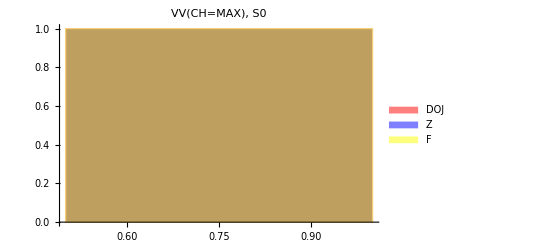
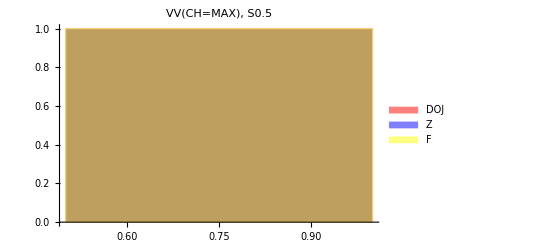
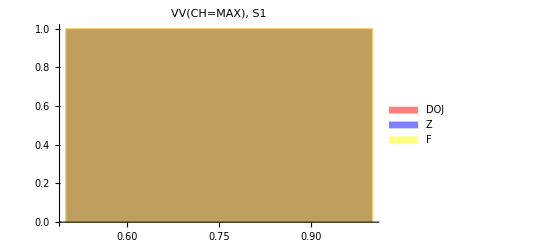
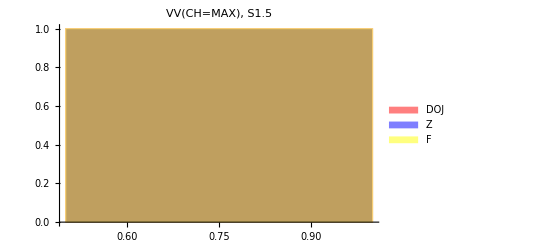
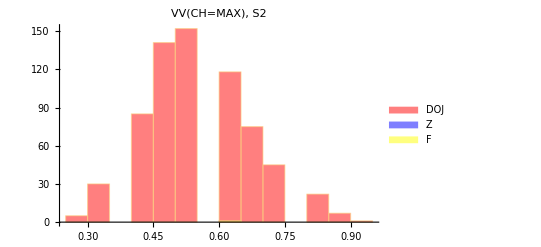
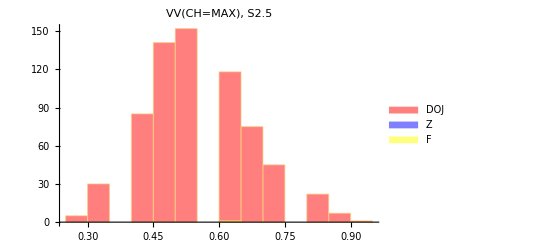
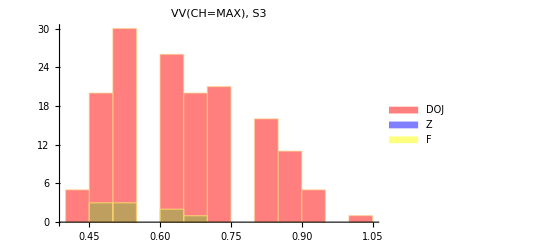
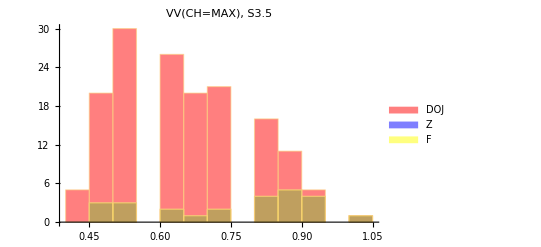
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | GrayLevel[1]

```mathematica
(*ListPlot[dojVVHist,PlotLegends->{"DOJ"},PlotStyle->{Red},PlotLabel->"VV CH=MAX geg EV&BK=DLB",PlotMarkers->{{"D",12}}, PlotRange->{0,1.05}]
ListPlot[zVVHist, PlotLegends->{"Z"},PlotStyle->{Blue},PlotLabel->"VV CH=MAX geg EV&BK=DLB",PlotMarkers->{{"Z",12}}, PlotRange->{0,1.05}]
ListPlot[fVVHist, PlotLegends->{"F"},PlotStyle->{Green},PlotLabel->"VV CH=MAX geg EV&BK=DLB",PlotMarkers->{{"F",12}}, PlotRange->{0,1.05}]
vvMaxPlot=ListPlot[{dojVVHist,zVVHist,fVVHist}, PlotLegends->{"DOJ","Z","F"},PlotStyle->{Red,Blue,Green},PlotLabel->"VV CH=MAX geg EV&BK=DLB",PlotMarkers->{{"D",12},{"Z",12},{"F",12}}, PlotRange->{0,1.05}]*)
timL={0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8};
Length[timL]
hist=Map[Histogram[{dojVV[[#,2]],zVV[[#,2]],fVV[[#,2]]}, PlotLabel->"VV(CH=MAX),    S"<>ToString[timL[[#]]],ImageSize->400, ChartLegends->{"DOJ","Z","F"},ChartStyle->{Red,Blue,Yellow}]&,Range[Length[timL]]];
histOut=Grid[{hist[[1;;3]],hist[[4;;6]],hist[[7;;9]],hist[[10;;12]],hist[[13;;15]],AppendTo[hist[[16;;17]],White]},ItemSize->35]
```

```mathematica
SetDirectory["/home/carla/GDC/CH_Pool/DLB/"];
(*Export["COMP_DOJ_CHTAT_CHMAX_DLB.jpeg",dojPlot,ImageResolution->300]
Export["COMP_CHTAT_CHMAX_DLB.jpeg",confMAX,ImageResolution->300]*)
Export["VV_CHMAX_HIST_DLB.jpeg",histOut,ImageResolution->300]
Put[dojVVHist, "gdc_DOJ_VV_CHMAX_DLB.txt"]
Put[zVVHist, "gdc_Z_VV_CHMAX_DLB.txt"]
Put[fVVHist, "gdc_F_VV_CHMAX_DLB.txt"]
```

VV_CHMAX_HIST_DLB.jpeg